```mathematica
Quantile[{0,1,2,3,4,5},0.7]
```

4

```mathematica
F[x_,μ_,σ_]:=1/(√(2π)*σ)*Integrate[ⅇ^((-(t-μ)^2)/(2 σ^2)),{t,-∞,x}]
```

ξ_1∼N(μ_1,σ_1^2),ξ_2∼N(μ_2,σ_2^2)
ξ_1+ξ_2∼N(μ_1+μ_2, σ_1^2+σ_2^2 +2 σ_1 σ_2 ρ)

```mathematica
μ1=3;
μ2=5;
σ1=2;
σ2=1;
ρ=0.3;
α=0.99;
```

```mathematica
F[22.42347,μ1+μ2,σ1^2+σ2^2+2σ1*σ2*ρ]
```

0.99

```mathematica
μ=3;
σ=2;
Clear[μ,σ]
{Quantile[NormalDistribution[μ,σ],0.99],Quantile[NormalDistribution[μ,σ],0.995]}
{Quantile[StudentTDistribution[10],0.99],Quantile[StudentTDistribution[10],0.995]}
{Quantile[LogNormalDistribution[μ,σ],0.99],Quantile[LogNormalDistribution[μ,σ],0.995]}
```

{μ+2.32635 σ,μ+2.57583 σ}

{2.76377,3.16927}

{ⅇ^(μ+2.32635 σ),ⅇ^(μ+2.57583 σ)}

2.32

```mathematica
f[x_]:=
```

```mathematica
D[1/(1+ⅇ^-x),x]
```

ⅇ^-x/((1+ⅇ^-x)^2)

```mathematica
Integrate[(x*ⅇ^-x)/((1+ⅇ^-x)^2),x]
```

x-x/(1+ⅇ^x)-Log[1+ⅇ^x]

```mathematica
Integrate[(1+ⅇ^-x),x]
```

-ⅇ^-x+x

```mathematica
Integrate[x/(1+ⅇ^-x),{x,0,1}]//N
```

0.329443

```mathematica
{x*(x-ⅇ^-x)+x^2/2+ⅇ^-x}/.{x->1}
```

{3/2}

```mathematica
{x*(x-ⅇ^-x)+x^2/2+ⅇ^-x}/.{x->0}
```

{1}

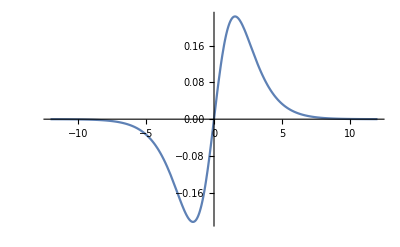

```mathematica
Plot[x*ⅇ^-x/((1+ⅇ^-x)^2),{x,-12,12}]
```

```mathematica
Integrate[(x^2*ⅇ^-x)/((1+ⅇ^-x)^2),{x,-∞,∞}]
```

π^2/3

```mathematica
-Log[1/0.9-1]
```

2.19722

```mathematica
μ1=3;
μ2=5;
σ1=2;
σ2=1;
ρ=0.3;
α=0.99;
```

```mathematica
Clear[μ1,μ2,σ1,σ2,ρ]
```

```mathematica
r = λ*μ1 + (1-λ)*μ2+√(λ^2 σ1^2-2 (-1+λ) λ ρ σ1 σ2+(-1+λ)^2 σ2^2)/FullSimplify
```

λ (μ1-μ2)+μ2+√(λ^2 σ1^2-2 (-1+λ) λ ρ σ1 σ2+(-1+λ)^2 σ2^2)

```mathematica
r
```

λ (μ1-μ2)+μ2+√(λ^2 σ1^2-2 (-1+λ) λ ρ σ1 σ2+(-1+λ)^2 σ2^2)

```mathematica
Minimize[{r, 0≤ λ≤1},λ]
```

$Aborted

```mathematica
Solve[D[r]==0,λ]
```

{{λ→(-μ1 μ2+μ2^2+ρ σ1 σ2-σ2^2-√(μ2^2 σ1^2-2 μ1 μ2 ρ σ1 σ2+μ1^2 σ2^2-σ1^2 σ2^2+ρ^2 σ1^2 σ2^2))/(μ1^2-2 μ1 μ2+μ2^2-σ1^2+2 ρ σ1 σ2-σ2^2)},{λ→(-μ1 μ2+μ2^2+ρ σ1 σ2-σ2^2+√(μ2^2 σ1^2-2 μ1 μ2 ρ σ1 σ2+μ1^2 σ2^2-σ1^2 σ2^2+ρ^2 σ1^2 σ2^2))/(μ1^2-2 μ1 μ2+μ2^2-σ1^2+2 ρ σ1 σ2-σ2^2)}}

```mathematica
F[x_,μ_,σ_]:=1/(√(2π)*σ)*Integrate[ⅇ^((-(t-μ)^2)/(2 σ^2)),{t,-∞,x}]
```

```mathematica
Solve[F[x,λ*μ1 + (1-λ)*μ2,√(λ^2 σ1^2-2 (-1+λ) λ ρ σ1 σ2+(-1+λ)^2 σ2^2)]==0,α]
```

$Aborted

```mathematica
NormalDistribution[]
```